```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"data"}]];
```

```mathematica
res=Table[Import[i, "Data"],{i,FileNames[]}];
```

```mathematica
Visualize[res_List,index_Integer,compared_List,name_String]:=
Module[
{},
ListLinePlot[Table[
Table[{i[[1]],i[[j]]},{i,res[[index]]}]
,{j,2,Length@(res[[index]][[1]])}]
,PlotLegends->compared,PlotLabel->Framed[name],LabelStyle->Directive[Black,Bold],Filling->Bottom,AxesLabel->{"iterations","time"},PlotRangePadding->None]
]
```

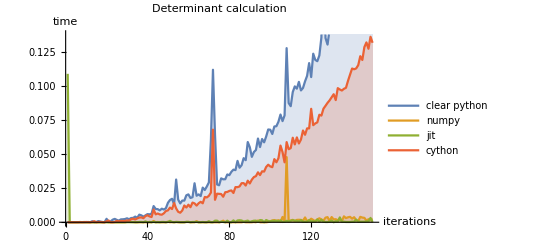

```mathematica
Visualize[res,1,{"clear python","numpy","jit","cython"},"Determinant calculation"]
```

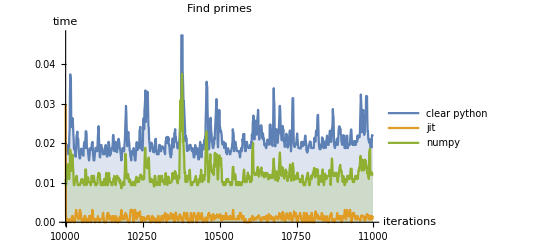

```mathematica
Visualize[res,2,{"clear python","jit","numpy"},"Find primes"]
```

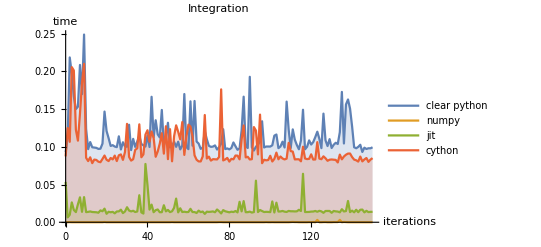

```mathematica
Visualize[res,3,{"clear python","numpy","jit", "cython"},"Integration"]
```

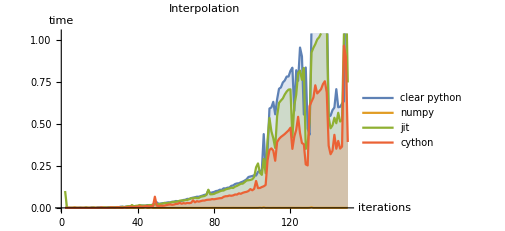

```mathematica
Visualize[res,4,{"clear python","numpy","jit", "cython"},"Interpolation"]
```

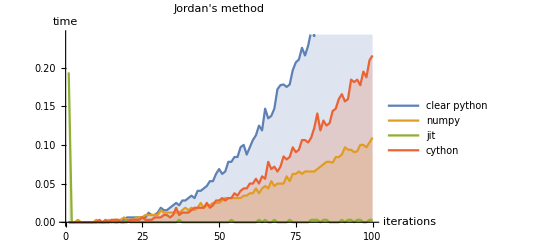

```mathematica
Visualize[res,5,{"clear python","numpy","jit","cython"},"Jordan's method"]
```

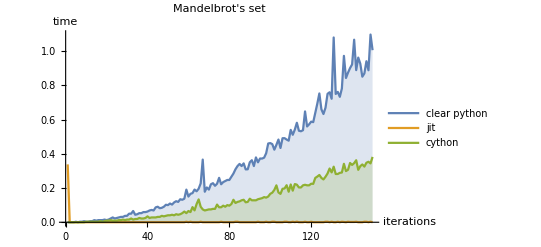

```mathematica
Visualize[res,6,{"clear python","jit","cython"},"Mandelbrot's set"]
```

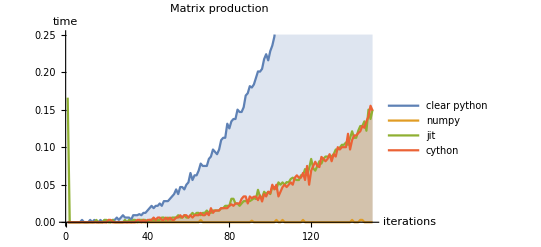

```mathematica
Visualize[res,7,{"clear python","numpy","jit","cython"},"Matrix production"]
```